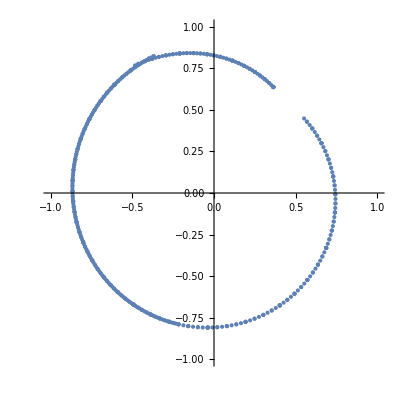

```mathematica
Remove[fnline,fnfact,rotate,intersect,start,stop,step,e,pdata];
fnline[n_]:=n*7;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
rotate[n_]:=(alpha=2*Pi*fnfact[n];x=-Sin[alpha];y=Cos[alpha];{x,y});
intersect[n_,e_]:=(line1={rotate[n],rotate[fnline[n]]};line2={rotate[n+e],rotate[fnline[n+e]]};a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];detx=Det[{{a12,det1},{a22,det2}}];dety=Det[{{det1,a11},{det2,a21}}];det=Det[{{a11,a12},{a21,a22}}];{detx/det,dety/det});

start=1;
stop=100;
step=0.2;
e=0.001;
pdata=Table[intersect[n,e],{n,start,stop,step}];
ListPlot[{pdata},PlotRange->{{-1,1},{-1,1}},AspectRatio->1]
```